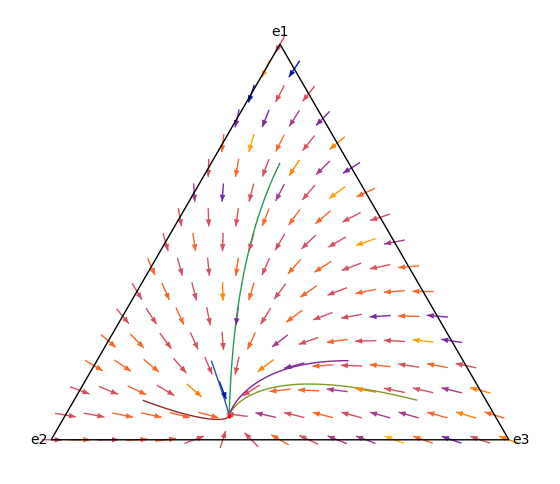

```mathematica
(* =====Dynamics on simplex x1+x2+x3==1 (x_i>=0)=====*)ClearAll[f1,f2,f3,XY,projSimplex,projTangent,arrow2D,rhs,sim];

(*Use (u,v)=(x2,x3);then x1=1-u-v keeps us on the simplex*)
f1[u_,v_]:=v^2-(1-u-v) (1+2 u);
f2[u_,v_]:=2 v^2+(1-u-v) (1+v)-u^2;
f3[u_,v_]:=2 (1-u-v) u-3 v^2-(1-u-v) v+u^2;  (* =-(f1+f2)*)

(*---Equilateral simplex with labels:e1 (top),e2 (left),e3 (right)---*)
v1={1/2.,Sqrt[3]/2.};   (*e1 (top)*)
v2={0.,0.};             (*e2 (left)*)
v3={1.,0.};             (*e3 (right)*)

(*Barycentric->2D:x={x1(top),x2(left),x3(right)}*)
XY[{x1_,x2_,x3_}]:=x1 v1+x2 v2+x3 v3;

(*Project a barycentric point back into the simplex (clip+renormalize)*)
projSimplex[{x1_,x2_,x3_}]:=Module[{x={x1,x2,x3}},x=Clip[x,{0,Infinity}];
If[Total[x]==0,{1,0,0},x/Total[x]]];

(*Project a 3D vector to the simplex tangent (zero-sum adjustment)*)
projTangent[{a_,b_,c_}]:=Module[{s=(a+b+c)/3.},{a-s,b-s,c-s}];

(*Build an in-simplex arrow at point p={x1,x2,x3}*)
stepScale=5.0;  (*larger->shorter arrows*)
arrow2D[p:{x1_,x2_,x3_}]:=Module[{u=x2,v=x3,vec3,vecT,nrm,p2},vec3={f1[u,v],f2[u,v],f3[u,v]};
vecT=projTangent[vec3];nrm=Norm[vecT];
p2=projSimplex[p+If[nrm==0,{0,0,0},vecT/(stepScale nrm)]];
XY[p2]-XY[p]];

(*-----Vector field (fewer arrows,all contained in the simplex)-----*)
n=16;  (*lower n=>fewer arrows;try 12..24*)
gridBary=N@Flatten[Table[{1-i-j,i,j},{i,0,1,1./n},{j,0,1-i,1./n}],1];
vfData={XY[#],arrow2D[#]}&/@gridBary;

vf=ListVectorPlot[vfData,VectorPoints->All,VectorStyle->GrayLevel[.25],VectorScale->Tiny,Axes->False,Frame->False,PlotRange->All];

(*-----Interior equilibrium (use (x2,x3)=(u,v))-----*)
eqUV=FindRoot[{f2[x2,x3]==0,f3[x2,x3]==0},{x2,0.5817},{x3,0.3588}];
xStar={1-x2-x3,x2,x3}/. eqUV//N;

eqGraphic=Graphics[{Red,PointSize[Large],Point[XY[xStar]]}];

(*-----Sample trajectories (RK4) in (x2,x3) with projection each substep-----*)
rhs[{x2_,x3_}]:=Module[{x1=1-x2-x3},{f2[x2,x3],f3[x2,x3]}];

projectUV[{x2_,x3_}]:=Module[{u=x2,v=x3},u=Max[u,0];v=Max[v,0];
If[u+v>1,{u,v}={u,v}/(u+v)];
{u,v}];

sim[{u0_,v0_},tmax_:8.,dt_:.02]:=Module[{u=u0,v=v0,t=0.,pts={{u0,v0}},k1,k2,k3,k4,y2,y3,y4},While[t<tmax,k1=rhs[{u,v}];
y2=projectUV[{u,v}+(dt/2) k1];k2=rhs[y2];
y3=projectUV[{u,v}+(dt/2) k2];k3=rhs[y3];
y4=projectUV[{u,v}+dt k3];k4=rhs[y4];
{u,v}=projectUV[{u,v}+(dt/6) (k1+2 k2+2 k3+k4)];
AppendTo[pts,{u,v}];t+=dt;];
pts];

startsUV={{.75,.15},{.15,.75},{.15,.15},{.55,.25},{.25,.55}};
pathsUV=sim[#,8,.02]&/@startsUV;
pathsXYZ=({1-#[[1]]-#[[2]],#[[1]],#[[2]]}&/@#)&/@pathsUV;
pathsXY=Line[XY/@#]&/@pathsXYZ;

colors=Table[Hue[(i-1)/Length[pathsXY],.75,.6],{i,Length[pathsXY]}];
traj=Graphics@MapThread[{#1,Thick,#2}&,{colors,pathsXY}];

(*-----Border+vertex labels:e1 top,e2 left,e3 right-----*)
border=Graphics[{Black,Thick,Line[{v2,v3,v1,v2}],Text[Style["e1",14],Offset[{0,12},v1]],(*up from the top*)Text[Style["e2",14],Offset[{-12,0},v2]],(*left from the left*)Text[Style["e3",14],Offset[{12,0},v3]]    (*right from the right*)}];

Show[vf,traj,eqGraphic,border,ImageSize->560,AspectRatio->Automatic,PlotRangePadding->0.05]
```

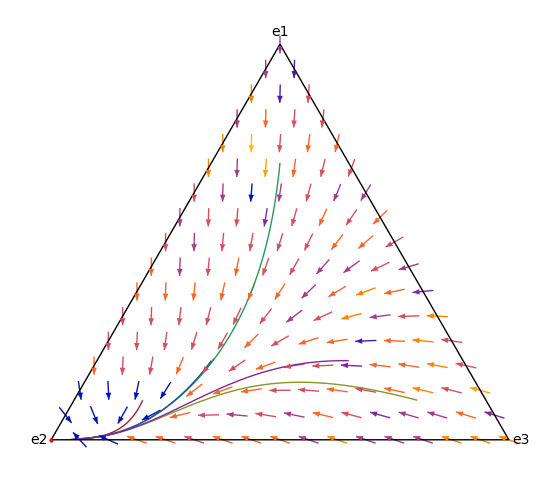

```mathematica
(* =====Dynamics on simplex x1+x2+x3==1 (x_i>=0)=====*)ClearAll[f1,f2,f3,XY,projSimplex,projTangent,arrow2D,rhs,sim];

(*Use (u,v)=(x2,x3);then x1=1-u-v keeps us on the simplex*)
f1[u_,v_]:=v^2-(1-u-v) (1+1-u-v+ u);
f2[u_,v_]:=2 v^2+(1-u-v) ;
f3[u_,v_]:=(1-u-v) (1-u-v+u)-3 v^2;  (* =-(f1+f2)*)

(*---Equilateral simplex with labels:e1 (top),e2 (left),e3 (right)---*)
v1={1/2.,Sqrt[3]/2.};   (*e1 (top)*)
v2={0.,0.};             (*e2 (left)*)
v3={1.,0.};             (*e3 (right)*)

(*Barycentric->2D:x={x1(top),x2(left),x3(right)}*)
XY[{x1_,x2_,x3_}]:=x1 v1+x2 v2+x3 v3;

(*Project a barycentric point back into the simplex (clip+renormalize)*)
projSimplex[{x1_,x2_,x3_}]:=Module[{x={x1,x2,x3}},x=Clip[x,{0,Infinity}];
If[Total[x]==0,{1,0,0},x/Total[x]]];

(*Project a 3D vector to the simplex tangent (zero-sum adjustment)*)
projTangent[{a_,b_,c_}]:=Module[{s=(a+b+c)/3.},{a-s,b-s,c-s}];

(*Build an in-simplex arrow at point p={x1,x2,x3}*)
stepScale=5.0;  (*larger->shorter arrows*)
arrow2D[p:{x1_,x2_,x3_}]:=Module[{u=x2,v=x3,vec3,vecT,nrm,p2},vec3={f1[u,v],f2[u,v],f3[u,v]};
vecT=projTangent[vec3];nrm=Norm[vecT];
p2=projSimplex[p+If[nrm==0,{0,0,0},vecT/(stepScale nrm)]];
XY[p2]-XY[p]];

(*-----Vector field (fewer arrows,all contained in the simplex)-----*)
n=16;  (*lower n=>fewer arrows;try 12..24*)
gridBary=N@Flatten[Table[{1-i-j,i,j},{i,0,1,1./n},{j,0,1-i,1./n}],1];
vfData={XY[#],arrow2D[#]}&/@gridBary;

vf=ListVectorPlot[vfData,VectorPoints->All,VectorStyle->GrayLevel[.25],VectorScale->Tiny,Axes->False,Frame->False,PlotRange->All];

(*-----Interior equilibrium (use (x2,x3)=(u,v))-----*)
eqUV=FindRoot[{f2[x2,x3]==0,f3[x2,x3]==0},{x2,0.5817},{x3,0.3588}];
xStar={1-x2-x3,x2,x3}/. eqUV//N;

eqGraphic=Graphics[{Red,PointSize[Large],Point[XY[xStar]]}];

(*-----Sample trajectories (RK4) in (x2,x3) with projection each substep-----*)
rhs[{x2_,x3_}]:=Module[{x1=1-x2-x3},{f2[x2,x3],f3[x2,x3]}];

projectUV[{x2_,x3_}]:=Module[{u=x2,v=x3},u=Max[u,0];v=Max[v,0];
If[u+v>1,{u,v}={u,v}/(u+v)];
{u,v}];

sim[{u0_,v0_},tmax_:8.,dt_:.02]:=Module[{u=u0,v=v0,t=0.,pts={{u0,v0}},k1,k2,k3,k4,y2,y3,y4},While[t<tmax,k1=rhs[{u,v}];
y2=projectUV[{u,v}+(dt/2) k1];k2=rhs[y2];
y3=projectUV[{u,v}+(dt/2) k2];k3=rhs[y3];
y4=projectUV[{u,v}+dt k3];k4=rhs[y4];
{u,v}=projectUV[{u,v}+(dt/6) (k1+2 k2+2 k3+k4)];
AppendTo[pts,{u,v}];t+=dt;];
pts];

startsUV={{.75,.15},{.15,.75},{.15,.15},{.55,.25},{.25,.55}};
pathsUV=sim[#,8,.02]&/@startsUV;
pathsXYZ=({1-#[[1]]-#[[2]],#[[1]],#[[2]]}&/@#)&/@pathsUV;
pathsXY=Line[XY/@#]&/@pathsXYZ;

colors=Table[Hue[(i-1)/Length[pathsXY],.75,.6],{i,Length[pathsXY]}];
traj=Graphics@MapThread[{#1,Thick,#2}&,{colors,pathsXY}];

(*-----Border+vertex labels:e1 top,e2 left,e3 right-----*)
border=Graphics[{Black,Thick,Line[{v2,v3,v1,v2}],Text[Style["e1",14],Offset[{0,12},v1]],(*up from the top*)Text[Style["e2",14],Offset[{-12,0},v2]],(*left from the left*)Text[Style["e3",14],Offset[{12,0},v3]]    (*right from the right*)}];

Show[vf,traj,eqGraphic,border,ImageSize->560,AspectRatio->Automatic,PlotRangePadding->0.05]
```

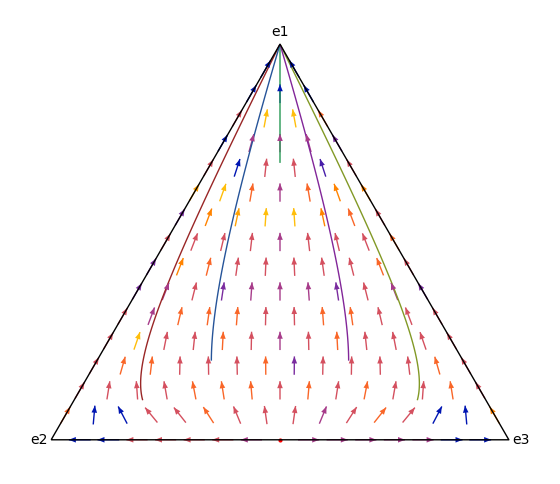

```mathematica
(* =====Dynamics on simplex x1+x2+x3==1 (x_i>=0)=====*)ClearAll[f1,f2,f3,XY,projSimplex,projTangent,arrow2D,rhs,sim];

(*Use (u,v)=(x2,x3);then x1=1-u-v keeps us on the simplex*)
f1[u_,v_]:=u (3 (1-u-v)^2+2 u (1-u-v)+3 v (1-u-v))+v (3 (1-u-v)^2+3 u (1-u-v)+2 v (1-u-v))-(1-u-v)(u^2+2u*v+v^2);

f2[u_,v_]:=(1-u-v) (u^2+u*v)+v  ((1-u-v) u+u^2)-u (3 (1-u-v)^2+(1-u-v) v+2 u (1-u-v)+3 v (1-u-v)+v^2);

f3[u_,v_]:=(1-u-v) (v^2+u*v)+u  ((1-u-v) v+v^2)-v (3 (1-u-v)^2+(1-u-v) u+2 v (1-u-v)+3 u (1-u-v)+u^2);


(*---Equilateral simplex with labels:e1 (top),e2 (left),e3 (right)---*)
v1={1/2.,Sqrt[3]/2.};   (*e1 (top)*)
v2={0.,0.};             (*e2 (left)*)
v3={1.,0.};             (*e3 (right)*)

(*Barycentric->2D:x={x1(top),x2(left),x3(right)}*)
XY[{x1_,x2_,x3_}]:=x1 v1+x2 v2+x3 v3;

(*Project a barycentric point back into the simplex (clip+renormalize)*)
projSimplex[{x1_,x2_,x3_}]:=Module[{x={x1,x2,x3}},x=Clip[x,{0,Infinity}];
If[Total[x]==0,{1,0,0},x/Total[x]]];

(*Project a 3D vector to the simplex tangent (zero-sum adjustment)*)
projTangent[{a_,b_,c_}]:=Module[{s=(a+b+c)/3.},{a-s,b-s,c-s}];

(*Build an in-simplex arrow at point p={x1,x2,x3}*)
stepScale=5.0;  (*larger->shorter arrows*)
arrow2D[p:{x1_,x2_,x3_}]:=Module[{u=x2,v=x3,vec3,vecT,nrm,p2},vec3={f1[u,v],f2[u,v],f3[u,v]};
vecT=projTangent[vec3];nrm=Norm[vecT];
p2=projSimplex[p+If[nrm==0,{0,0,0},vecT/(stepScale nrm)]];
XY[p2]-XY[p]];

(*-----Vector field (fewer arrows,all contained in the simplex)-----*)
n=16;  (*lower n=>fewer arrows;try 12..24*)
gridBary=N@Flatten[Table[{1-i-j,i,j},{i,0,1,1./n},{j,0,1-i,1./n}],1];
vfData={XY[#],arrow2D[#]}&/@gridBary;

vf=ListVectorPlot[vfData,VectorPoints->All,VectorStyle->GrayLevel[.25],VectorScale->Tiny,Axes->False,Frame->False,PlotRange->All];

(*-----Interior equilibrium (use (x2,x3)=(u,v))-----*)
eqUV=FindRoot[{f2[x2,x3]==0,f3[x2,x3]==0},{x2,0.5817},{x3,0.3588}];
xStar={1-x2-x3,x2,x3}/. eqUV//N;

eqGraphic=Graphics[{Red,PointSize[Large],Point[XY[xStar]]}];

(*-----Sample trajectories (RK4) in (x2,x3) with projection each substep-----*)
rhs[{x2_,x3_}]:=Module[{x1=1-x2-x3},{f2[x2,x3],f3[x2,x3]}];

projectUV[{x2_,x3_}]:=Module[{u=x2,v=x3},u=Max[u,0];v=Max[v,0];
If[u+v>1,{u,v}={u,v}/(u+v)];
{u,v}];

sim[{u0_,v0_},tmax_:8.,dt_:.02]:=Module[{u=u0,v=v0,t=0.,pts={{u0,v0}},k1,k2,k3,k4,y2,y3,y4},While[t<tmax,k1=rhs[{u,v}];
y2=projectUV[{u,v}+(dt/2) k1];k2=rhs[y2];
y3=projectUV[{u,v}+(dt/2) k2];k3=rhs[y3];
y4=projectUV[{u,v}+dt k3];k4=rhs[y4];
{u,v}=projectUV[{u,v}+(dt/6) (k1+2 k2+2 k3+k4)];
AppendTo[pts,{u,v}];t+=dt;];
pts];

startsUV={{.75,.15},{.15,.75},{.15,.15},{.55,.25},{.25,.55}};
pathsUV=sim[#,8,.02]&/@startsUV;
pathsXYZ=({1-#[[1]]-#[[2]],#[[1]],#[[2]]}&/@#)&/@pathsUV;
pathsXY=Line[XY/@#]&/@pathsXYZ;

colors=Table[Hue[(i-1)/Length[pathsXY],.75,.6],{i,Length[pathsXY]}];
traj=Graphics@MapThread[{#1,Thick,#2}&,{colors,pathsXY}];

(*-----Border+vertex labels:e1 top,e2 left,e3 right-----*)
border=Graphics[{Black,Thick,Line[{v2,v3,v1,v2}],Text[Style["e1",14],Offset[{0,12},v1]],(*up from the top*)Text[Style["e2",14],Offset[{-12,0},v2]],(*left from the left*)Text[Style["e3",14],Offset[{12,0},v3]]    (*right from the right*)}];

Show[vf,traj,eqGraphic,border,ImageSize->560,AspectRatio->Automatic,PlotRangePadding->0.05]
```

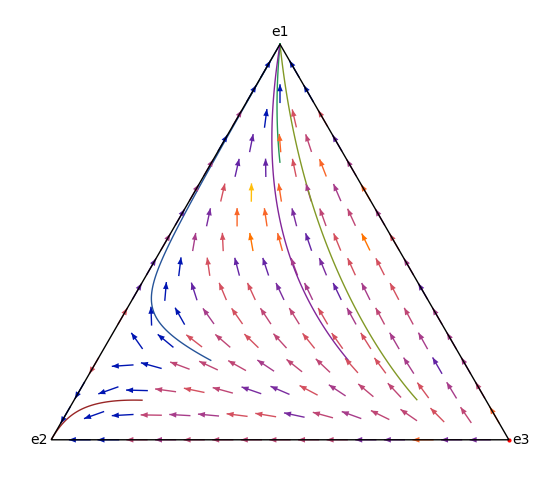

```mathematica
(* =====Dynamics on simplex x1+x2+x3==1 (x_i>=0)=====*)ClearAll[f1,f2,f3,XY,projSimplex,projTangent,arrow2D,rhs,sim];

(*Use (u,v)=(x2,x3);then x1=1-u-v keeps us on the simplex*)
f1[u_,v_]:=u (3 (1-u-v)^2+u (1-u-v)+3 v (1-u-v))+v (3 (1-u-v)^2+3 u (1-u-v)+2v(1-u-v))-(1-u-v)(2u^2+3u*v+v^2);

f2[u_,v_]:=(1-u-v) (2u^2+2u*v)+v  (2(1-u-v) u+2u^2+u*v)-u (3 (1-u-v)^2+(1-u-v) v+ u (1-u-v)+3 v (1-u-v)+v^2);

f3[u_,v_]:=(1-u-v) (v^2+u*v)+u  ((1-u-v) v+v^2)-v (3 (1-u-v)^2+2(1-u-v) u+2 v (1-u-v)+3 u (1-u-v)+2u^2+u*v);


(*---Equilateral simplex with labels:e1 (top),e2 (left),e3 (right)---*)
v1={1/2.,Sqrt[3]/2.};   (*e1 (top)*)
v2={0.,0.};             (*e2 (left)*)
v3={1.,0.};             (*e3 (right)*)

(*Barycentric->2D:x={x1(top),x2(left),x3(right)}*)
XY[{x1_,x2_,x3_}]:=x1 v1+x2 v2+x3 v3;

(*Project a barycentric point back into the simplex (clip+renormalize)*)
projSimplex[{x1_,x2_,x3_}]:=Module[{x={x1,x2,x3}},x=Clip[x,{0,Infinity}];
If[Total[x]==0,{1,0,0},x/Total[x]]];

(*Project a 3D vector to the simplex tangent (zero-sum adjustment)*)
projTangent[{a_,b_,c_}]:=Module[{s=(a+b+c)/3.},{a-s,b-s,c-s}];

(*Build an in-simplex arrow at point p={x1,x2,x3}*)
stepScale=5.0;  (*larger->shorter arrows*)
arrow2D[p:{x1_,x2_,x3_}]:=Module[{u=x2,v=x3,vec3,vecT,nrm,p2},vec3={f1[u,v],f2[u,v],f3[u,v]};
vecT=projTangent[vec3];nrm=Norm[vecT];
p2=projSimplex[p+If[nrm==0,{0,0,0},vecT/(stepScale nrm)]];
XY[p2]-XY[p]];

(*-----Vector field (fewer arrows,all contained in the simplex)-----*)
n=16;  (*lower n=>fewer arrows;try 12..24*)
gridBary=N@Flatten[Table[{1-i-j,i,j},{i,0,1,1./n},{j,0,1-i,1./n}],1];
vfData={XY[#],arrow2D[#]}&/@gridBary;

vf=ListVectorPlot[vfData,VectorPoints->All,VectorStyle->GrayLevel[.25],VectorScale->Tiny,Axes->False,Frame->False,PlotRange->All];

(*-----Interior equilibrium (use (x2,x3)=(u,v))-----*)
eqUV=FindRoot[{f2[x2,x3]==0,f3[x2,x3]==0},{x2,0.5817},{x3,0.3588}];
xStar={1-x2-x3,x2,x3}/. eqUV//N;

eqGraphic=Graphics[{Red,PointSize[Large],Point[XY[xStar]]}];

(*-----Sample trajectories (RK4) in (x2,x3) with projection each substep-----*)
rhs[{x2_,x3_}]:=Module[{x1=1-x2-x3},{f2[x2,x3],f3[x2,x3]}];

projectUV[{x2_,x3_}]:=Module[{u=x2,v=x3},u=Max[u,0];v=Max[v,0];
If[u+v>1,{u,v}={u,v}/(u+v)];
{u,v}];

sim[{u0_,v0_},tmax_:8.,dt_:.02]:=Module[{u=u0,v=v0,t=0.,pts={{u0,v0}},k1,k2,k3,k4,y2,y3,y4},While[t<tmax,k1=rhs[{u,v}];
y2=projectUV[{u,v}+(dt/2) k1];k2=rhs[y2];
y3=projectUV[{u,v}+(dt/2) k2];k3=rhs[y3];
y4=projectUV[{u,v}+dt k3];k4=rhs[y4];
{u,v}=projectUV[{u,v}+(dt/6) (k1+2 k2+2 k3+k4)];
AppendTo[pts,{u,v}];t+=dt;];
pts];

startsUV={{.75,.15},{.15,.75},{.15,.15},{.55,.25},{.25,.55}};
pathsUV=sim[#,8,.02]&/@startsUV;
pathsXYZ=({1-#[[1]]-#[[2]],#[[1]],#[[2]]}&/@#)&/@pathsUV;
pathsXY=Line[XY/@#]&/@pathsXYZ;

colors=Table[Hue[(i-1)/Length[pathsXY],.75,.6],{i,Length[pathsXY]}];
traj=Graphics@MapThread[{#1,Thick,#2}&,{colors,pathsXY}];

(*-----Border+vertex labels:e1 top,e2 left,e3 right-----*)
border=Graphics[{Black,Thick,Line[{v2,v3,v1,v2}],Text[Style["e1",14],Offset[{0,12},v1]],(*up from the top*)Text[Style["e2",14],Offset[{-12,0},v2]],(*left from the left*)Text[Style["e3",14],Offset[{12,0},v3]]    (*right from the right*)}];

Show[vf,traj,eqGraphic,border,ImageSize->560,AspectRatio->Automatic,PlotRangePadding->0.05]
```